```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

### 渦電流の計算

```mathematica
Pin=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]](*Point input*)
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

```mathematica
Pin=Delete[{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}},{{1},{27},{32},{2},{48},{6},{51},{46},{11},{38},{5},{49},{9},{12},{47},{18},{4},{17},{37}}]
```

{{52,64},{17,63},{31,62},{51,21},{5,25},{12,42},{36,16},{52,41},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{43,67},{58,48},{58,27},{37,69},{46,10},{61,33},{62,63},{63,69},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{56,37}}

```mathematica
GOrigin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];(* Ginの元のグラフ *)
```

```mathematica
PDOrigin=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[GOrigin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[GOrigin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[GOrigin]]}];(* Point Distance Origin *)
```

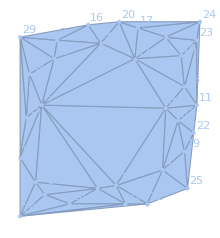

{26→27,27→5,5→26,26→9,9→27,5→15,15→29,29→5,6→15,5→6,27→6,9→28,28→30,30→9,26→28,27→30,30→6,31→7,7→30,30→31,28→31,26→31,7→6,14→6,6→13,13→14,14→15,29→13,13→2,2→29,29→14,6→3,3→13,2→3,3→16,16→2,20→16,3→20,3→12,12→20,16→29,6→12,8→6,7→8,21→4,4→7,7→21,21→31,26→21,4→8,4→32,32→8,21→25,25→4,8→12,19→25,25→22,22→19,19→32,4→19,32→11,11→8,22→32,22→11,12→10,10→1,1→12,12→18,18→10,17→1,1→24,24→17,17→12,10→23,23→1,17→20,18→11,11→23,23→18,8→18,23→24,11→24,24→20}

```mathematica
DelaunayMesh[Pin];
HighlightMesh[%,Labeled[0,"Index"]]
Ruleg=EdgeRulesMesh[%]
```

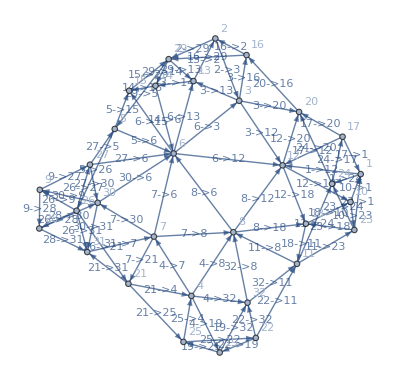

```mathematica
Gin=Graph[Ruleg,VertexLabels->"Name",EdgeLabels->"Name"](*Ggraph input*)
```

```mathematica
FundLoop=FindFundamentalCycles[UndirectedGraph[Gin]];
```

```mathematica
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
```

```mathematica
RuleRevFundLoop=Table[EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],{i,Length[FundLoop]}];
```

```mathematica
h=Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[Gin]}
],
{j,Length[FundLoop]}] ;(* 検算済 *)
```

```mathematica
PD=PDDelaunay=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
```

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]//N].(h.s+U)
```

{-3.77992,-3.49844,6.64091,-0.97574,-1.76015,-4.15523,-2.52428,4.08919,1.35624,-1.89492,0.105986,1.65882,0.423442,0.874408,2.65581,-2.14762,-13.6264,8.00195,-9.019,2.00878,3.89118,4.37693,9.41013,-3.51229,9.34301,-6.06468,0.274708,2.81349,1.5837,-0.815233,2.8271,-5.81434,-16.6375,26.2851,32.3136,23.8861,4.64184,23.6852,-18.8906,-74.2214,13.0693,-6.8916,7.51078,18.2079,3.3816,5.55891,-5.03813,-2.27494,4.36383,38.7433,-7.59373,167.077,-1.78095,12.4666,20.3718,1.88152,-12.366,33.1387,10.3969,-20.8603,-109.717,-121.39,54.5561,-100.061,13.6264,5.58825,-16.4661,12.0842,5.8223,-11.9298,7.45172,3.09139,-26.6342,13.8604,-2.67291,41.6554,69.1633,-12.9868,-11.8539,74.7553,15.4004,-6.23814,13.5226}

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U)
```

$Aborted

```mathematica
Curr//N
```

{11.7688+0.000168828 (0.+Re[NDSolve`FEM`FEMNBoundaryIntegrate[1,{MeasureDump`X$30630[1],MeasureDump`X$30630[2]},Polygon[{{37.,69.},{52.,64.},{43.,67.}}]]]),10.8004+1,492,1,9.68614-0.0000178325 (0.+Re[NDSolve`FEM`FEMNBoundaryIntegrate[1,{MeasureDump`X$104385[1],20[2]},Polygon[{{37.,69.},{52.,64.},{43.,67.}}]]])}
 |  |  |  |

```mathematica
Graphics[Point[{{25,55},{37,52},{49,49}}]]
```

-Graphics-

```mathematica
Graphics[Polygon[{{25,55},{37,52},{49,49}}]]
```

-Graphics-

```mathematica
Area[Polygon[{{25,55},{37,52},{49,49}}]]
```

Area[Polygon[{{25,55},{37,52},{49,49}}]]

```mathematica
Curr
```

{11.7688+0.000168828 Area[Polygon[{{37,69},{52,64},{43,67}}]],10.8004+0.000363929 Area[Polygon[{{37,69},{52,64},{43,67}}]],492,7.7713-0.0000194922 Area[Polygon[{{37,69},{52,64},{43,67}}]],9.68614-0.0000178325 Area[Polygon[{{37,69},{52,64},{43,67}}]]}
 |  |  |  |

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gout]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

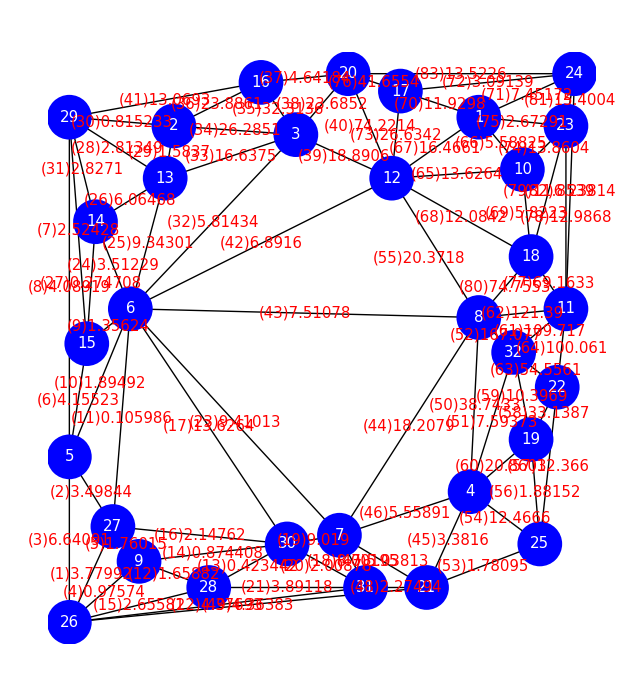

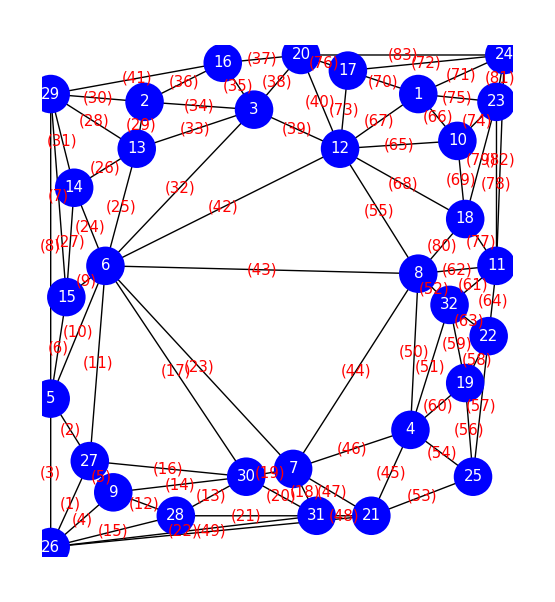

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

26→27 | 27→5 | 5→26 | 26→9 | 9→27 | 5→15 | 15→29 | 29→5 | 6→15 | 5→6
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

27→6 | 9→28 | 28→30 | 30→9 | 26→28 | 27→30 | 30→6 | 31→7 | 7→30 | 30→31
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

28→31 | 26→31 | 7→6 | 14→6 | 6→13 | 13→14 | 14→15 | 29→13 | 13→2 | 2→29
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

29→14 | 6→3 | 3→13 | 2→3 | 3→16 | 16→2 | 20→16 | 3→20 | 3→12 | 12→20
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

16→29 | 6→12 | 8→6 | 7→8 | 21→4
41 | 42 | 43 | 44 | 45

```mathematica
CurrRank=Ordering[Abs[1/Curr ]](* 昇順 *)
```

{52,62,61,64,80,40,77,63,76,50,58,35,73,34,36,38,60,55,39,44,33,67,81,74,65,17,83,41,78,54,57,68,70,79,59,23,25,19,18,51,43,71,42,3,82,26,69,32,66,46,47,37,22,49,6,8,21,1,24,2,45,72,31,28,75,15,7,48,16,20,10,56,53,5,12,29,9,4,14,30,13,27,11}

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{3.19664,2.69663,2.86106,10.8944,2.84067,3.1654,10.3304,9.53733,4.72122,9.70213,236.634,5.15066,24.3141,19.5758,6.20995,9.35907,2.38141,0.838321,0.674439,5.12531,4.62584,7.82157,3.76016,3.06647,1.66158,1.55556,51.093,4.63425,3.84085,14.7707,4.37526,4.74452,0.950347,0.533979,0.22316,0.468068,2.16507,0.389253,0.639634,0.175152,1.71093,4.86694,5.32734,1.63016,3.57318,2.84433,2.31473,3.077,9.44002,0.516863,2.20749,0.0338579,7.82076,0.802145,0.926182,6.39992,1.46456,0.202428,0.980871,0.441966,0.0711853,0.0827901,0.117368,0.0904988,1.10325,1.39762,0.741312,1.51914,1.7261,0.795224,1.62151,6.50185,0.377329,0.510162,3.7599,0.15183,0.104262,1.61703,1.30963,0.12333,0.394974,4.33118,1.92271}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{52,61,62,64,77,63,80,76,40,58,35,73,38,81,60,36,74,50,34,39,19,67,70,54,18,55,33,59,65,79,66,57,68,26,78,71,44,25,41,69,83,37,51,47,17,2,5,46,3,24,48,6,1,45,75,23,29,82,31,21,28,9,32,42,20,12,43,15,56,72,53,22,16,49,8,10,7,4,30,14,13,27,11}

```mathematica
FindShortestTour[Pin,PerformanceGoal->"Speed"]
Graphics[Line[Pin[[Last[%]]]]]
```

{17+9 √2+11 √5+2 √10+4 √13+3 √17+2 √29+3 √37+2 √41+√73+2 √85+√89+3 √101+√106+√113+2 √146+√149+√170+√173+√194,{1,24,23,10,18,11,8,32,22,19,4,25,21,31,7,30,28,9,26,27,5,15,6,14,29,13,2,16,3,20,17,12,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法4

```mathematica
GreedyDirectedPartLoop[CurrRank]
```

{32→8,8→11,11→32}

```mathematica
GreedyDirectedPartLoop[PDCurrCostSort]
```

{32→8,8→11,11→32}

```mathematica
PartLoop1={32->8,8->11,11->32};
```

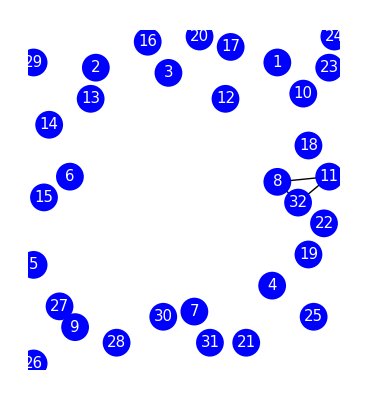

{20→3,3→22,22→2,2→20}

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,PartLoop1}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
PartLoopProcess
```

{{2->16,16->29,29->20,20->2}}

{2,20,29,16,2}

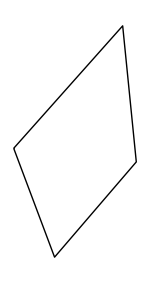

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
MostOutEdge[PartLoop1,PDCurrCostSort]
```

114

```mathematica
OutEdgeList
```

{136,117,122,133,119,137,114,134,139,115,118,113,121,141}

```mathematica
OutEdgeRank[PartLoop1,PDCurrCostSort]
```

{101,86,82,116,105,64,114,104,128,61,115,108,98,111,106,135,67,52,99,84,46,102,23,53,63,68,25,137,136,26,118,40,58,88,127,122,54,74,131,66,130,100,70,120,121,73,24,113,85,80,119,69,126,139,138,20,117,89,50,34,76,56,75,36,2,123,59,81,8,97,77,60,41,42,35,45,103,110,124,92,38,16,96,55,5,47,93,9,72,71,14,87,65,3,39,90,12,15,33,107,13,18,22,28,109,4,21,11,43,78,51,37,49,31,95,29,7,79,62,134,83,1,44,112,6,57,10,30,27,48,32,19,91,17,94}

```mathematica
PluralPartLoopByGreedyFromRank2[OutEdgeRank[PartLoop1,PDCurrCostSort]]
```

{49→9,9→38,38→49}

```mathematica
FirstPosition[OutEdgeRank[PartLoop1,PDCurrCostSort],55]
```

{84}

```mathematica
EdgeRules[Gout][[OutEdgeRank[PartLoop1,PDCurrCostSort]]]
```

{49→9,38→49,5→49,22→1,34→21,48→8,2→11,34→50,21→29,46→51,22→2,9→34,30→34,1→32,50→21,35→20,8→1,23→48,49→30,11→38,6→23,9→38,37→44,7→48,48→26,1→27,15→37,35→36,35→3,17→37,28→22,14→25,27→6,16→38,16→21,3→22,26→7,32→27,29→35,1→48,21→35,49→10,48→6,8→22,3→28,32→46,44→15,1→2,11→5,15→5,28→31,27→48,20→22,21→36,36→3,44→17,31→22,11→46,23→7,12→5,45→15,6→14,37→5,46→12,41→19,36→28,51→6,49→15,13→41,39→34,45→33,27→51,24→14,25→24,46→5,24→6,30→9,50→16,36→31,11→32,51→47,25→13,33→39,26→43,19→42,43→24,10→39,13→40,31→26,31→8,47→18,11→16,26→8,41→40,51→12,10→15,18→13,18→25,6→18,9→50,47→4,42→17,44→45,17→12,9→16,40→42,42→45,18→4,14→18,33→15,43→7,40→45,43→23,12→37,10→30,12→47,4→41,40→33,27→46,20→3,5→38,19→40,23→24,32→2,4→19,43→13,4→13,4→17,17→47,25→43,47→6,42→44,33→10,42→4,30→39}

```mathematica
PartLoop2=InsertVertex[PartLoop1,3]
```

{2→1,5→4,4→2,1→3,3→5}

{1,2,4,5,3,1}

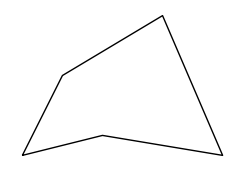

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[line=Line[Pin[[%]]]]
```